# Arnoldi Iteration (Cont)

How and why does the Arnoldi eigenvalue work? We have a lot of slightly fancy machinery.  We construct and are looking in the Krylov space
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By definition any x∈𝒦_n(A,b)  satisfies x=c_0 b+c_1 A.b+ c_2 A^2.b+…+c_(n-1)A^(n-1).b=q(A).b where q(A) is the polynomial
	q(A)=c_0 Id+c_1 A+ c_2 A^2+…+c_(n-1)A^(n-1).
The question is what do we gain by writing/thinking of this as in terms of matrix polynomials!

We will see that the polynomial implicitly built by Arnoldi and other Krylov methods is the best polynomial in a very specific sense which gives convergence information.

## Polynomial Lemniscate

A lemniscate of a polynomial p(z) are the level sets of |p(z)|=c.  You can plot these. They can be complicated.

```mathematica
p[z_]:=8.9-4 z-3 z^2+6 z^3-7 z^4+2 z^6+9 z^7+6 z^8-2 z^9
ContourPlot[ Abs[p[x+ I y]], {x, -1.5,1},{y,-1.2,1.2},
ContourLabels->All,
PlotPoints->100,
Epilog->{Red, Point[ReIm[NSolveValues[p[z]==0,z]]]},
Contours->{1,2,3,4,5,6,7,8,9,10}]
```

-Graphics-

You can see the zeros sitting in the middle of each blob.  Once the contours are small enough the blobs separate. Eventually if the roots are isolated each root is in one blob!

## Arnoldi Reminder

Just as a reminder: The Arnoldi process iteratively computes a nested sequence of orthogonal matrices Q_n∈ℝ^(m×n) and rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n).  Columns of Q_n are an orthonormal basis for the Krylov space	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By construction, A maps 𝒦_n(A,b)→𝒦_(n+1)(A,b) with H_n the matrix for this map in the orthogonal basis. In other words, since H_n is Upper Hessenberg
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
If the bottom corner of H_n is zero the Q_n is an invariant space of A and eigenvalues of the square Upper Hessenberg matrix
	(Ĥ)_n=H_n[1:n,1:n]
are eigenvalues of A.  Hopefully when H_n[n+1,n] is small the eigenvalues of (Ĥ)_n are close to eigenvalues of A.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Remember:

Eigenvalues of (Ĥ)_n are the n roots of the characteristic polynomial p_n(z)=det(z I - (Ĥ)_n).

The eigenvalues λ_1,…,λ_n of (Ĥ)_n (called Ritz values or Arnoldi Approximations) approximate eigenvalues of A.

The matching eigenvector approximations v_i=Q_n.𝓋_i for i in (where (Ĥ)_n.𝓋_i=λ_i 𝓋_i) are called Ritz vectors.

## Arnoldi Lemniscate

The Arnoldi lemniscate is simply
	det(z I - (Ĥ)_n)=p_n(z)=||p_n(A).b||/||b||.
 As n gets bigger two things happen: the degree of the polynomial increases and hopefully the right hand side gets smaller.  Eventually (if we wait until n=m) the right hand side goes to zero and leaves the characteristic polynomial for the m eigenvalues of A.

Arnoldi detects “large” eigenvalues first.  Here is a test matrix with three “designed” large eigenvalues!

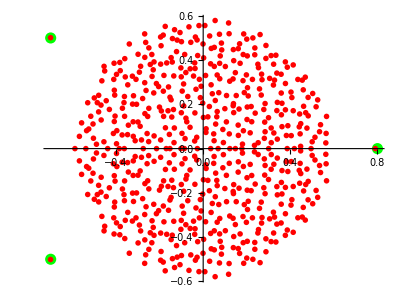

```mathematica
m=600;
A=RandomReal[{-1/√m,1/√m},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={0.8,-0.7,0.5};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
EValPic=ListPlot[{ReIm[Eigenvalues[AExtra]],ReIm[Eigenvalues[A]]},
PlotRange->All,
PlotStyle->{{Green, PointSize[0.02]},{Red,PointSize[0.01]}},
AspectRatio->Automatic]
```

Lets see what the Arnoldi lemniscate pictures look like for this.

```mathematica
Clear[MaxIter,Q0,H0,HData,p,c,n,z,PolyData]
MaxIter=15;
b=Normalize[RandomReal[{-1,1},m]];
{Q0,H0}={{b}ᵀ,{{}}};
HData=NestList[Arnoldi[A],{Q0,H0},MaxIter]⟦2;;MaxIter,2⟧;
TabView[Map[MatrixPlot,HData],MaxIter-1];
Clear[p,n]
TabView[
Table[
H=HData⟦n⟧;
p[n][z_]=CharacteristicPolynomial[H⟦1;;n⟧,z];
c[n]=Norm[p[n][A].b];
{p[n][z],c[n],H⟦-1,-1⟧},
{n,1, Length[HData]}],Length[HData]];
TabView[
Table[ 
Show[EValPic,
ContourPlot[Abs[p[n][x+I y]]==c[n],{x,-1,1},{y,-0.7,0.7},
PlotPoints->200]],
{n, 1, Length[HData]}]
]
```

1234567891011121314

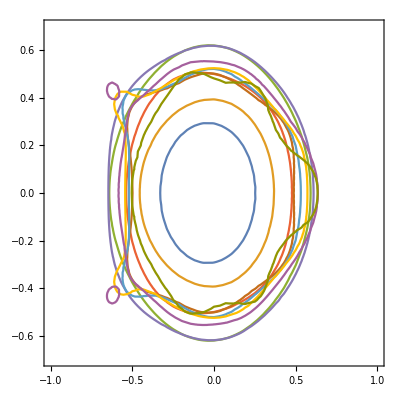

```mathematica
ContourPlot[{
Abs[p[2][x+I y]]==c[2],
Abs[p[3][x+I y]]==c[3],
Abs[p[4][x+I y]]==c[4],
Abs[p[5][x+I y]]==c[5],
Abs[p[6][x+I y]]==c[6],
Abs[p[7][x+I y]]==c[7],
Abs[p[8][x+I y]]==c[8],
Abs[p[9][x+I y]]==c[9],
Abs[p[10][x+I y]]==c[10],
Abs[p[11][x+I y]]==c[11],
Abs[p[12][x+I y]]==c[12]
},{x,-1,1},{y,-0.7,0.7}]
```

Old Stuff

## Arnoldi Eigenvalues

The Arnoldi iteration can continue as long as w≠0 after projecting out all the previous directions. If w=0 then Q describes an invariant space for A and A.Q=Q.ℋ where ℋ is simply the square Upper Hessenberg upper block of H.  If this happens the eigenvalues of ℋ are eigenvalues of A. The bottom element of H does not need to be zero for the eigenvalues of ℋ (called Ritz values or Arnoldi estimates) to be useful approximations to large eigenvalues of A.

If we look at the Ritz values we can see them converge. In this case a cartoon is worth a lot of words.

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];
EvalPic=ListPlot[ReIm[Eigenvalues[A]],
PlotRange->All,PlotStyle->{Green,PointSize[0.02]},
AspectRatio->Automatic,
Frame->True];
MaxIter=m;
b=RandomReal[{-1,1},m];
{Q0,H0}={{Normalize[b]}ᵀ,{{}}};
HData=NestList[Arnoldi[A],{Q0,H0},MaxIter]⟦2;;-1,2,1;;-2⟧;
RitzValues=Map[Eigenvalues,HData];
TableForm[RitzValues];
k=23;
ListAnimate[Map[
Show[EvalPic,Epilog->{Red, PointSize[0.015],Point[ReIm[#]]}]&,RitzValues],
6]
```

This with appropriate refinements and flourishes is what almost all eigenvalue algorithms for sparse non-symmetric matrices do.